# Short time displacements

## compute displacements

```mathematica
DIM=2;
boxInvTrans[boxmat_,pt_]:=Module[{invmat},
invmat=Inverse[boxmat];
invmat.pt
];
boxTrans[boxmat_,pt_]:=boxmat.pt;
putInBox[boxmat_,pt_]:=Module[{temp},
temp=boxInvTrans[boxmat,pt];
Do[
If[Between[temp[[dd]]==False,{0,1}],temp[[dd]]-=Sign[temp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,temp]
];
minDist[boxmat_,ptA_,ptB_]:=Module[{vA,vB,disp},
vA=boxInvTrans[boxmat,ptA];
vB=boxInvTrans[boxmat,ptB];
disp=vA-vB;
Do[
If[Abs[disp[[dd]]]>0.5,disp[[dd]]-=Sign[disp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,disp]
];
```

```mathematica
computeDisplacements[inipts_,pts_,boxmat_]:=Module[{minDists,minLenths,overlaps},
minDists=Table[minDist[boxmat,inipts[[i]],pts[[i]]],{i,1,Length[pts]}]
];
```

## load data

```mathematica
temperatures={"0.06300000","0.00500000","0.00200000"};
```

```mathematica
data=Table[Import["C:\\Users\\cheng\\Downloads\\glassyDynamics_N4096_p3.8250_T"<>temp<>"_waitingTime10000_idx10.nc","Data"],{temp,temperatures}];
```

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825/displacementField_N4096_p3.8250_T0.00050000_id15.nc","Data"]
```

<|/displacementsField→NumericArray[<641,8192>, Real64],/time→NumericArray[…]|>

```mathematica
Partition[Normal[data[[1,120,;;]]],2][[;;10]]
```

{{-0.132385,1.43445},{-1.62887,0.512456},{-0.196067,0.731246},{-0.298966,-0.454135},{2.28152,0.188694},{0.752863,-0.995264},{-0.33733,-0.0539205},{0.324404,0.120403},{0.0256056,0.136009},{-0.527003,0.42131}}

```mathematica
Partition[Normal[data[[1,1,;;]]],2][[1]]
```

{30.0715,50.1399}

```mathematica
Normal[data[[2,;;,1]]]
```

{101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101778.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101779.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101780.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101781.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101782.,101783.,101783.,101783.,101783.,101783.,101783.,101783.,101783.,101783.,101784.,101784.,101784.,101784.,101784.,101784.,101784.,101784.,101785.,101785.,101785.,101785.,101785.,101785.,101786.,101786.,101786.,101786.,101786.,101786.,101787.,101787.,101787.,101787.,101787.,101788.,101788.,101788.,101788.,101789.,101789.,101789.,101789.,101789.,101790.,101790.,101790.,101791.,101791.,101791.,101791.,101792.,101792.,101792.,101793.,101793.,101793.,101794.,101794.,101794.,101795.,101795.,101796.,101796.,101796.,101797.,101797.,101798.,101798.,101799.,101799.,101800.,101800.,101801.,101801.,101802.,101802.,101803.,101803.,101804.,101805.,101805.,101806.,101806.,101807.,101808.,101808.,101809.,101810.,101811.,101811.,101812.,101813.,101814.,101815.,101815.,101816.,101817.,101818.,101819.,101820.,101821.,101822.,101823.,101824.,101825.,101826.,101827.,101828.,101830.,101831.,101832.,101833.,101835.,101836.,101837.,101839.,101840.,101841.,101843.,101844.,101846.,101847.,101849.,101851.,101852.,101854.,101856.,101858.,101860.,101861.,101863.,101865.,101867.,101869.,101872.,101874.,101876.,101878.,101881.,101883.,101885.,101888.,101890.,101893.,101896.,101899.,101901.,101904.,101907.,101910.,101913.,101916.,101920.,101923.,101926.,101930.,101933.,101937.,101940.,101944.,101948.,101952.,101956.,101960.,101964.,101969.,101973.,101978.,101982.,101987.,101992.,101997.,102002.,102007.,102013.,102018.,102024.,102029.,102035.,102041.,102047.,102054.,102060.,102067.,102073.,102080.,102087.,102095.,102102.,102109.,102117.,102125.,102133.,102141.,102150.,102158.,102167.,102176.,102186.,102195.,102205.,102215.,102225.,102235.,102246.,102257.,102268.,102279.,102291.,102303.,102315.,102328.,102341.,102354.,102367.,102381.,102395.,102409.,102424.,102439.,102454.,102470.,102486.,102503.,102520.,102537.,102555.,102573.,102591.,102610.,102629.,102649.,102670.,102690.,102712.,102733.,102756.,102778.,102802.,102825.,102850.,102875.,102900.,102926.,102953.,102981.,103009.,103037.,103067.,103097.,103127.,103159.,103191.,103224.,103257.,103292.,103327.,103363.,103400.,103438.,103477.,103516.,103557.,103598.,103640.,103684.,103728.,103774.,103820.,103868.,103916.,103966.,104017.,104069.,104123.,104177.,104233.,104290.,104349.,104409.,104470.,104533.,104597.,104662.,104729.,104798.,104869.,104941.,105014.,105090.,105167.,105246.,105326.,105409.,105494.,105580.,105669.,105759.,105852.,105947.,106044.,106143.,106245.,106349.,106456.,106565.,106676.,106790.,106907.,107026.,107149.,107274.,107402.,107533.,107667.,107804.,107944.,108088.,108235.,108385.,108539.,108697.,108858.,109023.,109191.,109364.,109541.,109722.,109907.,110096.,110290.,110488.,110691.,110898.,111111.,111328.,111551.,111778.,112011.,112250.,112493.,112743.,112998.,113260.,113527.,113801.,114081.,114368.,114661.,114961.,115268.,115582.,115904.,116233.,116569.,116914.,117266.,117627.,117996.,118374.,118761.,119156.,119561.,119975.,120399.,120833.,121277.,121731.,122196.,122671.,123158.,123656.,124165.,124687.,125221.,125767.,126325.,126897.,127482.,128081.,128694.,129321.,129962.,130619.,131290.,131978.,132681.,133401.,134138.,134891.,135663.,136452.,137260.,138086.,138932.,139797.,140683.,141589.,142516.,143465.,144436.,145430.,146447.,147487.,148552.,149641.,150756.,151897.,153064.,154259.,155481.,156732.,158012.,159322.,160663.,162034.,163438.,164874.,166344.,167848.,169387.,170961.,172573.,174222.,175909.,177636.,179403.,181211.,183061.,184955.,186892.,188875.,190903.,192979.,195104.,197278.,199502.,201778.,204108.,206491.,208930.,211426.,213980.,216594.,219268.,222005.,224805.,227671.,230603.,233604.,236675.,239817.,243032.,246322.,249689.,253134.,256660.,260268.,263959.,267737.,271603.,275558.,279606.,283748.,287987.,292324.,296763.,301305.,305952.,310708.,315574.,320554.,325650.,330865.,336201.,341662.,347249.,352967.,358818.,364805.,370932.,377201.,383617.,390181.,396899.,403773.,410808.,418006.,425372.,432909.,440622.,448515.,456592.,464856.,473314.,481968.,490823.,499885.}

```mathematica
temperatures
```

{0.06300000,0.00500000,0.00200000}

```mathematica
Norm[{0.5,0.5}]
```

0.707107

```mathematica
displacements=Partition[Normal[data[[1,641,;;]]],2];
```

```mathematica
displacements=Table[Table[computeDisplacements[Partition[Normal[data[[temp,3,1]]],2],Partition[Normal[data[[temp,3,time]]],2],Partition[Normal[data[[1,1,1]]],2]],{time,2,Length[data[[1,1]]]}],{temp,3}];
```

```mathematica
magnitudes=Table[Table[Norm/@displacements[[i,time]],{time,Length[data[[1,1]]]-1}],{i,3}];
```

Part::partw: Part 3 of {{0.441931,1.05225},{-0.48089,-0.236669},{0.659376,-0.121272},{-1.02039,0.130537},{1.75744,0.00167408},{1.73864,0.314448},{-0.571916,0.833102},{-0.531123,0.886902},{0.439801,-0.071871},{-0.222232,-1.11387},«4086»} does not exist.

Part::partd: Part specification 38.1833⟦1,3⟧ is longer than depth of object.

Part::partw: Part 4 of {{0.441931,1.05225},{-0.48089,-0.236669},{0.659376,-0.121272},{-1.02039,0.130537},{1.75744,0.00167408},{1.73864,0.314448},{-0.571916,0.833102},{-0.531123,0.886902},{0.439801,-0.071871},{-0.222232,-1.11387},«4086»} does not exist.

Part::partd: Part specification 38.1833⟦1,4⟧ is longer than depth of object.

Part::partw: Part 5 of {{0.441931,1.05225},{-0.48089,-0.236669},{0.659376,-0.121272},{-1.02039,0.130537},{1.75744,0.00167408},{1.73864,0.314448},{-0.571916,0.833102},{-0.531123,0.886902},{0.439801,-0.071871},{-0.222232,-1.11387},«4086»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 38.1833⟦1,5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Max[magnitudes[[1,10]]]
```

Part::partd1: Depth of object {0.0481236,0.0231099,0.00444354,0.00893507,0.0108659,0.0189777,0.0126896,0.0536399,0.0901555,0.0253825,«4086»} is not sufficient for the given part specification.

```mathematica
ListVectorPlot
```

```mathematica
magnitudes=Norm/@displacements;
```

```mathematica
Mean[magnitudes]
```

4.41843

```mathematica
ListDensityPlot[Table[Flatten[{Partition[Normal[data[[1,1,;;]]],2][[i]],magnitudes[[i]]}],{i,4096}],ImageSize->400,ColorFunction->Hue]
```

-Graphics-

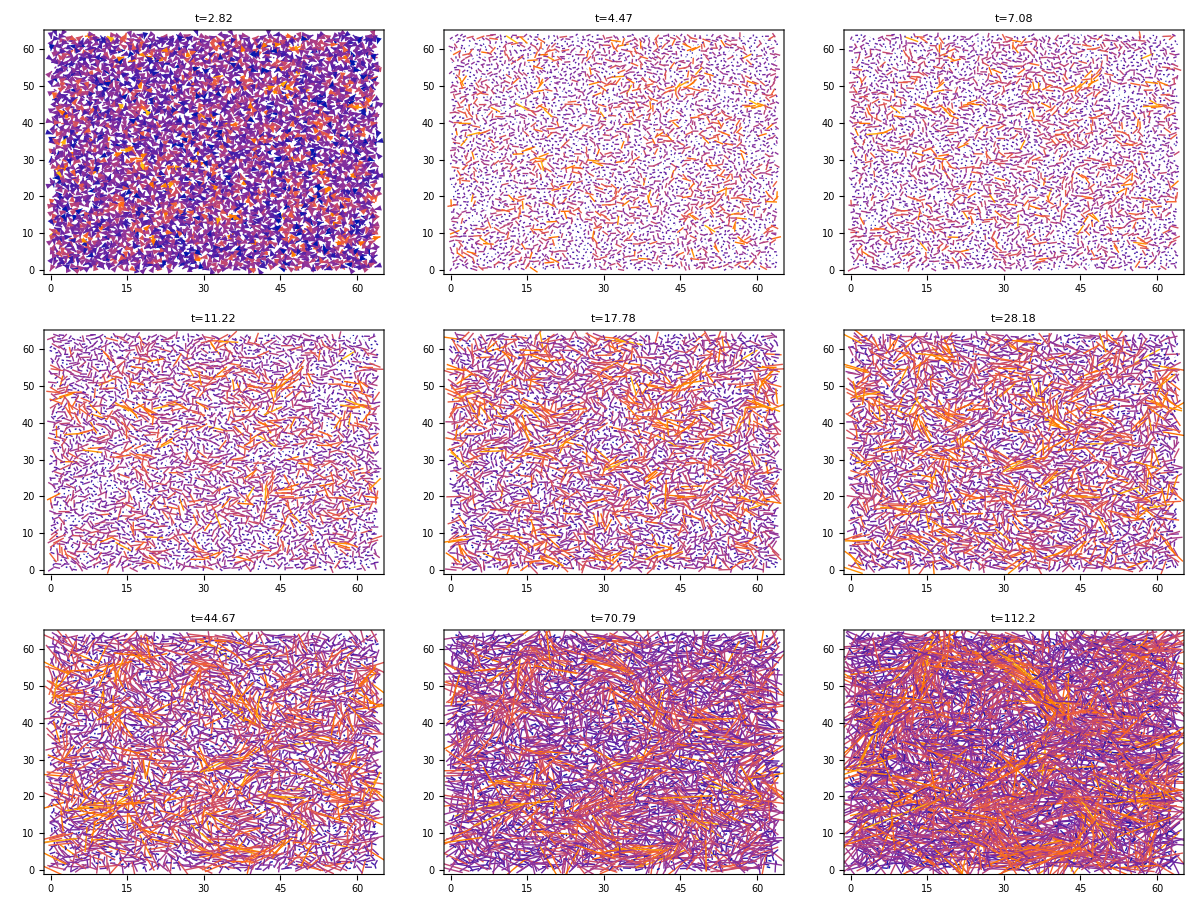

```mathematica
Grid[Partition[Table[ListVectorPlot[Table[{Partition[Normal[data[[1,3,1]]],2][[i]],displacements[[1,time,i]]},{i,4096}],VectorSizes->{0,Max[magnitudes[[1,time]]]},VectorScaling->"Linear",VectorStyle->{Thin,Arrowheads[0.01]},VectorPoints->All,VectorColorFunctionScaling->True,PlotLabel->"t="<>ToString[data[[1,4,time,1]]-data[[1,4,1,1]]],ImageSize->400],{time,40,73,4}],3]]
```

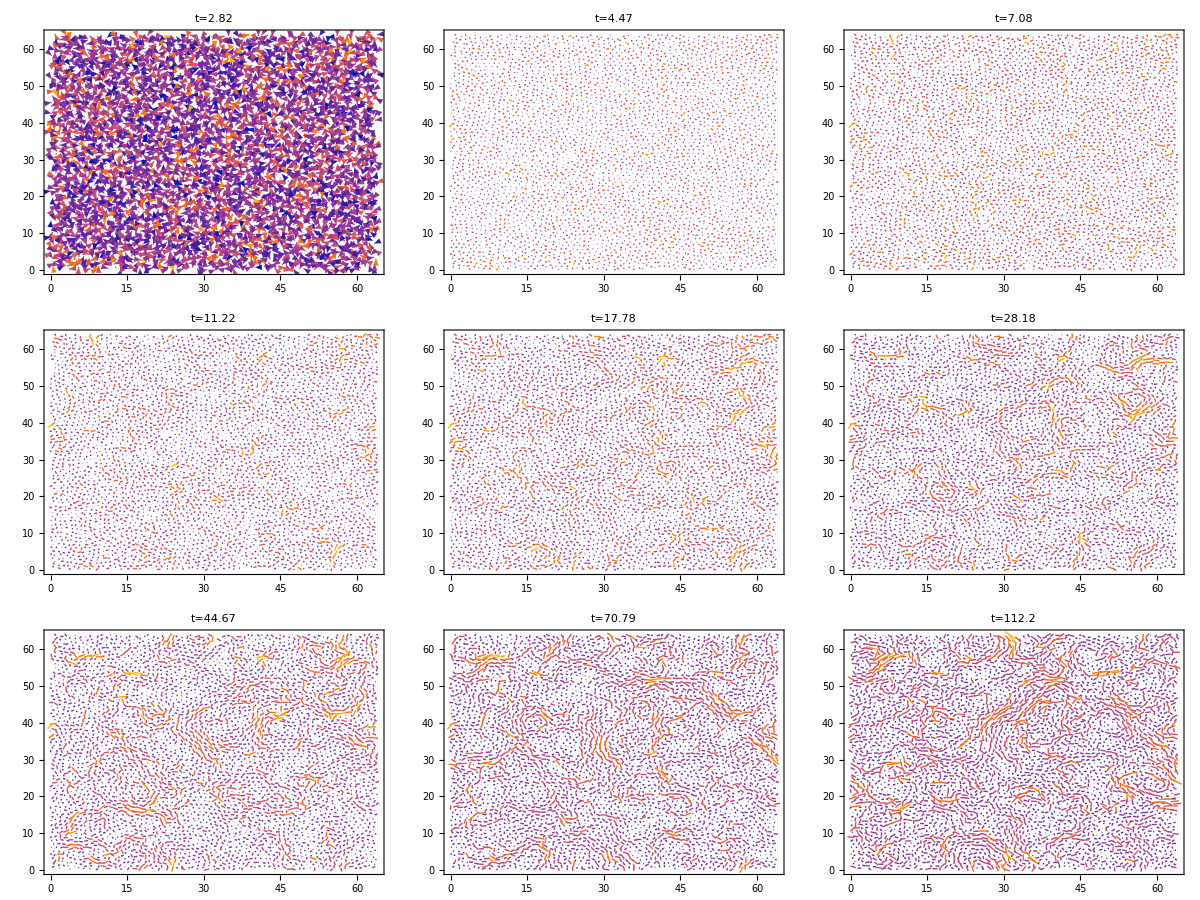

```mathematica
Grid[Partition[Table[ListVectorPlot[Table[{Partition[Normal[data[[2,3,1]]],2][[i]],displacements[[2,time,i]]},{i,4096}],VectorSizes->{0,Max[magnitudes[[2,time]]]},VectorScaling->"Linear",VectorStyle->{Thin,Arrowheads[0.01]},VectorPoints->All,VectorColorFunctionScaling->True,PlotLabel->"t="<>ToString[data[[2,4,time,1]]-data[[2,4,1,1]]],ImageSize->400],{time,40,73,4}],3]]
```